Name: GDM_2D_PA.nb
Author: CCL
Date: November 2014
Description: This script generates a 2D Penrose tiling using the generalized dual method. It can also generate a periodic approximant.

```mathematica
tau=(1+Sqrt[5])/2; (*golden ratio*)
tau=3/2;
numlines=20;
tolerance=10^-10;
```

```mathematica
a=2Pi/5;
A=tau-1;
r1={1,0,0};
r2={Cos[a],Sin[a],0};
Or3={Cos[2a],Sin[2a],0};
Or4={Cos[3a],Sin[3a],0};
Or5={Cos[4a],Sin[4a],0};
r3=Normalize[-r1+A r2];
r4=Normalize[-A(r1+r2)];
r5=Normalize[-r2+A r1];
starvectors={r1,r2,r3,r4,r5};
origvectors={r1,r2,Or3,Or4,Or5};
numvectors=Length[starvectors];
startuples=Select[Tuples@{Range[numvectors],Range[numvectors]},Less@@#&];
starbasis =Graphics3D[Arrow[{{0,0,0},#}]&/@starvectors,Axes->True];
origstarbasis =Graphics3D[Arrow[{{0,0,0},#}]&/@origvectors,Axes->True];
xyBasis =Graphics[Arrow[{{0,0},#}]&/@{{1,0},{0,1}},Axes->True];
axes =Graphics3D[Arrow[{{0,0,0},#}]&/@{{1,0,0},{0,1,0},{0,0,1}},Axes->True];
```

```mathematica
PeriodicSeq=Range[-numlines/2,numlines/2];
spacings=PeriodicSeq;
```

```mathematica
p1=0.01;
p2=0.02;
p3=-p1+A p2;
p4=-A(p1+p2);
p5=A p1 - p2;
Phases={p1,p2,p3,p4,p5};
ShiftedSpacings=Table[i+j,{i,Phases},{j,spacings}]
```

{{-9.99,-8.99,-7.99,-6.99,-5.99,-4.99,-3.99,-2.99,-1.99,-0.99,0.01,1.01,2.01,3.01,4.01,5.01,6.01,7.01,8.01,9.01,10.01},{-9.98,-8.98,-7.98,-6.98,-5.98,-4.98,-3.98,-2.98,-1.98,-0.98,0.02,1.02,2.02,3.02,4.02,5.02,6.02,7.02,8.02,9.02,10.02},{-10.,-9.,-8.,-7.,-6.,-5.,-4.,-3.,-2.,-1.,0.,1.,2.,3.,4.,5.,6.,7.,8.,9.,10.},{-10.015,-9.015,-8.015,-7.015,-6.015,-5.015,-4.015,-3.015,-2.015,-1.015,-0.015,0.985,1.985,2.985,3.985,4.985,5.985,6.985,7.985,8.985,9.985},{-10.015,-9.015,-8.015,-7.015,-6.015,-5.015,-4.015,-3.015,-2.015,-1.015,-0.015,0.985,1.985,2.985,3.985,4.985,5.985,6.985,7.985,8.985,9.985}}

```mathematica
maxlength=N[Min[Table[Table[Abs[spacing/Abs[starvectors[[i]]].{1,1,0}],{spacing,{ShiftedSpacings[[i,1]],ShiftedSpacings[[i,numlines+1]]}}],{i,Range[numvectors]}]]];
Print["maxlength = ",maxlength];
```

maxlength = 7.14847

```mathematica
(*this function finds intersection point of three grid lines, where e_i denotes star vector, and n_i denotes line number*)
FindIntersection[{n1_,e1_},{n2_,e2_},{n3_,e3_}]:=Module[
{p1,p2,p3,d},
p1=n1*e1;
p2=n2*e2;
p3=n3*e3;
d=Det[{e1,e2,e3}];
If[d==0,{0,0,0},
Chop[N[1/d*
((p1.e1)Cross[e2,e3]+(p2.e2)Cross[e3,e1]+(p3.e3)Cross[e1,e2]),{Infinity,150}]]]
]
```

```mathematica
(* ULTIMATE FUNCTION *)
(* finds intersections, with tuples of the form
{{m,n},{i,j},{x,y,z}} = {{indices of spacings},{indices of star vectors},{intersection point}} *)
pts=Table[
{{m,n},
{pair[[1]],pair[[2]]},
FindIntersection[{ShiftedSpacings[[pair[[1]],m]],starvectors[[pair[[1]]]]},{ShiftedSpacings[[pair[[2]],n]],starvectors[[pair[[2]]]]},{0,{0,0,1}}]
},
{m,Range[numlines+1]},{n,Range[numlines+1]},{pair,startuples}];
pts=Flatten[pts,2];
pts=pts[[Ordering[pts[[All,3,2]]]]];
Print[Length[pts]];
```

4410

```mathematica
CountInstances[inlist_,tol_]:=Module[
{poslist,uniqposlist,spacelist,starlist,out,counts,len,uniqlen,counter,curelem,curcompare,i,j},
poslist=inlist[[All,3]];
counts={};
uniqposlist={};
spacelist={};
starlist={};
out={};
len=Length[poslist];
For[i=1,i≤len,i++,
curelem=poslist[[i]];
(*-1 indicates already counted*)
If[TrueQ[curelem==-1],
Continue[];,
uniqposlist=Append[uniqposlist,curelem];
spacelist=Append[spacelist,inlist[[i,1]]];
starlist=Append[starlist,inlist[[i,2]]];
];
counter=1;
For[j=i+1,j≤len,j++,
curcompare=poslist[[j]];
If[TrueQ[curcompare==-1],Continue[];];
If[Norm[poslist[[j]]-curelem]<tol,
poslist[[j]]=-1;(*sets to -1 if counted*)
counter=counter+1;
]
];
counts=Append[counts,counter];
];
uniqlen=Length[uniqposlist];
For[i=1,i≤uniqlen,i++,
out=Append[out,{spacelist[[i]],starlist[[i]],uniqposlist[[i]],counts[[i]]}];
];
out
]
UniqueGridVertices=CountInstances[pts,tolerance];
Print[Length[UniqueGridVertices]];
```

4388

```mathematica
UniqueGridVertices[[1]]
```

{{1,1},{1,3},{-9.99,-38.1615,0},1}

## Find dual of grid intersections, the quasilattice

```mathematica
(*takes a point and finds the indices of the surrounding grid lines*)
FindGridIndices[x_]:=Module[
{gridindices,curindex,curvector,i},
gridindices={};
Do[
curvector=starvectors[[i]];
curindex=Min[Flatten[Position[ShiftedSpacings[[i]],_?(Chop[#-x.curvector]≥0&)],1]];
(*returns {} if outside bounds of spacings*)
If[TrueQ[curindex==∞],
gridindices={};
Return[{}];
,
gridindices=Append[gridindices,curindex];
];
,{i,Range[numvectors]}
];
Return[gridindices];
]
```

```mathematica
(*constructs PROTOTILE*)
FindProtoTile[vertex_,i_,j_]:=Module[
{v,tile,pair},
v=Table[vertex+y,{y,
{0,origvectors[[i]],origvectors[[j]],
origvectors[[i]]+origvectors[[j]]
}}];
v=v[[All,{1,2}]];
tile=Graphics[Line[{
{v[[1]],v[[2]]},
{v[[1]],v[[3]]},
{v[[2]],v[[4]]},
{v[[3]],v[[4]]}
}]];
pair={i,j};
{tile,pair}
]
```

```mathematica
(*constructs ZONOTILE*)
eps=10^-3;
UpDown={-1,1};
ProbeIndices=Tuples[{UpDown,UpDown,UpDown,UpDown,UpDown}];
ProbeVectors=N[Table[eps*Normalize[n.starvectors],{n,ProbeIndices}]];

FindZonoTile[vertex_,x_]:=Module[
{GridIndices,UniqueGridIndices,curindex,probe,len,i,j,CurDiff,StarIndex,vertexpair,EdgeIndices,EdgeCoords,VertexCoords,tile,tuple},

(*find grid indices for surrounding open regions*)
GridIndices={};
Do[
curindex=FindGridIndices[x+probe];
(*Print[curindex];*)
If[TrueQ[curindex=={}],
Return[{{},{}}];,
GridIndices=Append[GridIndices,curindex];
];
,{probe,ProbeVectors}
];
UniqueGridIndices=Sort[DeleteDuplicates[GridIndices]];
len=Length[UniqueGridIndices];
If[TrueQ[len==0],Return[{{},{}}];];
(*Print[len];*)

(*go through finding connected vertices, and get vertex coordinates*)
EdgeIndices={};
EdgeCoords={};
VertexCoords=ConstantArray[0,len];
VertexCoords[[1]]=vertex;

For[i=1,i≤len,i++,
For[j=i+1,j≤len,j++,
CurDiff=UniqueGridIndices[[j]]-UniqueGridIndices[[i]];
If[Count[CurDiff,1]==1&&Count[CurDiff,-1]==0,
(*Print[i,", ",j,": ",UniqueGridIndices[[i]],", ", UniqueGridIndices[[j]]];*)
StarIndex=Flatten[Position[CurDiff,1]][[1]];
VertexCoords[[j]]=VertexCoords[[i]]+origvectors[[StarIndex]];(*identifies vertex coordinate*)
EdgeIndices=Append[EdgeIndices,{i,j}];
];
];
];

VertexCoords=VertexCoords[[All,{1,2}]];
(*construct tile*)
Do[
EdgeCoords=Append[EdgeCoords,{VertexCoords[[vertexpair[[1]]]],VertexCoords[[vertexpair[[2]]]]}];
,{vertexpair,EdgeIndices}
];
tile=Graphics[Line[EdgeCoords]];

(*find tuple of star vectors*)
tuple={};
For[i=1,i≤numvectors,i++,
If[Length[Tally[UniqueGridIndices[[All,i]]]]>1,
tuple=Append[tuple,i];
]
];

{tile,tuple}
]
(*testtile=FindTile[UniqueGridVertices[[633]]]*)
```

```mathematica
FindTile[pt_]:=Module[
{l,m,i,j,x,count,vertex,tile,tuple,v,indices},
l=pt[[1,1]];
m=pt[[1,2]];
i=pt[[2,1]];
j=pt[[2,2]];
x=pt[[3]];
count=pt[[4]];
If[Abs[x[[1]]]<maxlength&&Abs[x[[2]]]<maxlength&&Abs[x[[3]]]<maxlength,
indices=FindGridIndices[x];
If[TrueQ[indices!={}]&&VectorQ[N[indices.origvectors],NumericQ],
vertex=N[indices.origvectors];
If[TrueQ[count==1],
{tile,tuple}=FindProtoTile[vertex,i,j];,
{tile,tuple}=FindZonoTile[vertex,x];
];
If[TrueQ[tuple=={}],
Return[];
];
(*Print[pt,tile];*)
Return[{vertex,tile,tuple}]
];

];

Return[];
]
tiles=Select[Table[FindTile[pt],{pt,UniqueGridVertices}],UnsameQ[#,Null]&];
```

Part::partd: Part specification {{-1.77636×10^-15, 0., 0.}, 0, {1/4\ (-1 + √5), √5/8 + √5/8, 0}, {1., 0., 0.}, 0, {1/4\ (-1 - √5), √5/8 - √5/8, 0}} ⟦ All, {1, 2} ⟧ is longer than depth of object.

Part::partw: Part 4 of {{-1.77636×10^-15, 0., 0.}, 0, {1/4\ (-1 + √5), √5/8 + √5/8, 0}, {1., 0., 0.}, 0, {1/4\ (-1 - √5), √5/8 - √5/8, 0}} ⟦ All, {1, 2} ⟧ does not exist.

Part::partw: Part 6 of {{-1.77636×10^-15, 0., 0.}, 0, {1/4\ (-1 + √5), √5/8 + √5/8, 0}, {1., 0., 0.}, 0, {1/4\ (-1 - √5), √5/8 - √5/8, 0}} ⟦ All, {1, 2} ⟧ does not exist.

Part::partw: Part 5 of {{-1.77636×10^-15, 0., 0.}, 0, {1/4\ (-1 + √5), √5/8 + √5/8, 0}, {1., 0., 0.}, 0, {1/4\ (-1 - √5), √5/8 - √5/8, 0}} ⟦ All, {1, 2} ⟧ does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

## Plotting

```mathematica
Module[
{i,counts},
counts=Table[Length[tiles[[x,3]]],{x,Range[1,Length[tiles]]}];
For[i=5,i≥0,i--,
Print["# tiles formed form intersection of ", i, " grid lines: ", Count[counts,i]];
]
]
```

# tiles formed form intersection of 5 grid lines: 0

# tiles formed form intersection of 4 grid lines: 1

# tiles formed form intersection of 3 grid lines: 8

# tiles formed form intersection of 2 grid lines: 1568

# tiles formed form intersection of 1 grid lines: 0

# tiles formed form intersection of 0 grid lines: 0

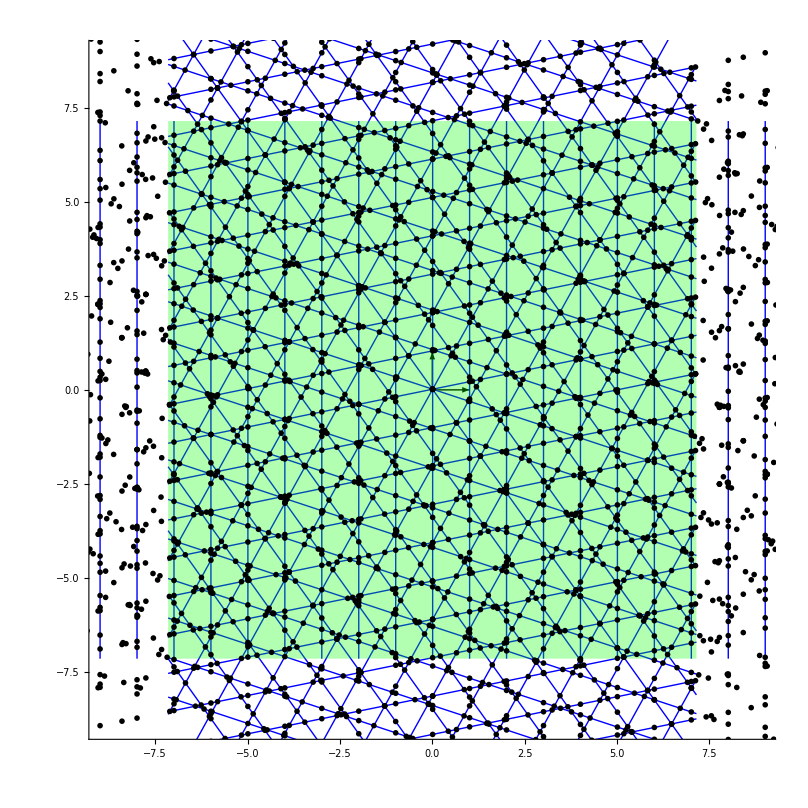

```mathematica
Show[xyBasis,
Table[Plot[-starvectors[[i,1]]/starvectors[[i,2]]*x+ShiftedSpacings[[i,j]]/starvectors[[i,2]],{x,-maxlength,maxlength},PlotStyle->{Blue,Thin}],{i,Range[2,5]},{j,Range[numlines+1]}],
Table[Graphics[{Blue,Thin,Line[{{x,-maxlength},{x,maxlength}}]}],{x,ShiftedSpacings[[1]]}],
Graphics[{Green,Opacity[0.3],Polygon[{{-maxlength,-maxlength},{-maxlength,maxlength},{maxlength,maxlength},{maxlength,-maxlength},{-maxlength,-maxlength}}]}],
Graphics[{PointSize[0.005],Point[UniqueGridVertices[[All,3,{1,2}]]]}](*option here gets rid of indeterminate values*),
Graphics[{PointSize[0.001],Red,Point[UniqueGridVertices[[186,3,{1,2}]]]}],
AspectRatio->1,PlotRange->{{-1.25maxlength,1.25maxlength},{-1.25maxlength,1.25maxlength}}
]
```

```mathematica
(*translate vertices and tiles so that COM is at origin*)
CalculateCOM[pts_]:=Module[
{x,y},
x=0;y=0;
Do[
x+=pt[[1]];y+=pt[[2]];,
{pt,pts}];
{x,y}/Length[pts]
]
com=CalculateCOM[Flatten[tiles[[All,2,1,1]],2]];
tiles2=tiles;
tiles2[[All,1]]=Table[x-com,{x,tiles2[[All,1,{1,2}]]}];
translate={com,com};
Do[
tiles2[[i,2,1,1]]=Table[x-translate,{x,tiles2[[i,2,1,1,All]]}];
,{i,Length[tiles2]}
]
```

Part::partd: Part specification All ⟦ 1 ⟧ is longer than depth of object.

Part::partd: Part specification All ⟦ 2 ⟧ is longer than depth of object.

Thread::tdlen: Objects of unequal length in {{-1.77636×10^-15, 0., 0.}, 0, {1/4\ (-1 + √5), √5/8 + √5/8, 0}, {1., 0., 0.}, 0, {1/4\ (-1 - √5), √5/8 - √5/8, 0}} + {{27.4164  - All ⟦ 1 ⟧ - 4\ {« 6 »} ⟦ All, {« 2 »} ⟧/12648, 27.4164  - All ⟦ 1 ⟧ - 4\ {« 6 »} ⟦ All, {« 2 »} ⟧/12648, 27.4164  - All ⟦ 1 ⟧ - 4\ {« 6 »} ⟦ All, {« 2 »} ⟧/12648}, 426.038  - All ⟦ 2 ⟧/12648} cannot be combined.

```mathematica
allvertices=Module[
{list,n},
list={};
n=Length[tiles2];
Do[
list=Join[list,Flatten[tiles2[[i,2,1,1]],1]];
,{i,Range[n]}
];
list
];
```

```mathematica
tiles2[[1]]
```

{{{-13.7082+(27.4164-All⟦1⟧-4 {{-1.77636×10^-15,0.,0.},0,{1/4 (-1+√5),√(5/8+(√5)/8),0},{1.,0.,0.},0,{1/4 (-1-√5),√(5/8-(√5)/8),0}}⟦All,{1,2}⟧)/12648,-13.7082+(27.4164-All⟦1⟧-4 {{-1.77636×10^-15,0.,0.},0,{1/4 (-1+√5),√(5/8+(√5)/8),0},{1.,0.,0.},0,{1/4 (-1-√5),√(5/8-(√5)/8),0}}⟦All,{1,2}⟧)/12648,-13.7082+(27.4164-All⟦1⟧-4 {{-1.77636×10^-15,0.,0.},0,{1/4 (-1+√5),√(5/8+(√5)/8),0},{1.,0.,0.},0,{1/4 (-1-√5),√(5/8-(√5)/8),0}}⟦All,{1,2}⟧)/12648},-18.0171+(426.038-All⟦2⟧)/12648},-Graphics-,{3,5}}

```mathematica
GraphicsRow[
{
Show[xyBasis,
(*tiles2[[All,2]],*)
(*Graphics[{PointSize[0.01],Blue,Point[allvertices]}],*)
Graphics[{{PointSize[0.01],Red,Point[tiles2[[All,1]]]},
{PointSize[Large],Blue,Point[tiles2[[Flatten[Position[tiles2[[All,3]],_?(Length[#]==3&)],2],1]]]},
{PointSize[Large],Green,Point[tiles2[[Flatten[Position[tiles2[[All,3]],_?(Length[#]==2&)],2],1]]]}
}],
AspectRatio->1,ImageSize->600
],
Show[xyBasis,
tiles2[[All,2]],
Graphics[{PointSize[0.01],Red,Point[tiles2[[All,1]]]}],
AspectRatio->1,ImageSize->600
]
}]
```

-Graphics-